# Eigenvectors and Eigenfunctions

An eigenvector is a normalized list of numbers.

An eigenfunction is a normalized function.

If you export the mass matrix M and stiffness matrix A for a 2D ODE from Fenics and/or Julia they are associated with a list of m nodes (where A and M are m×m matrices) in a mesh i.e. {x_1,y_1},…,{x_m,y_m}. To plot the eigenfunctions you need to associate each value v_1,v_2,…,v_m in an eigenvector A.v=λ M.v with its matching node.  There are lots of ways to do this.  I am going to demo this a few ways in Mathematica using (just cause I want to see what the efuns look like) an equilateral triangle.

Note: We did this algebraically and as a plot when we built the matrices in Mathematica

## Very Small Mesh

Here is a very coarse mesh with labelled vertices.

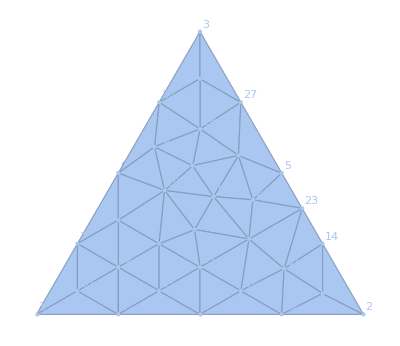

```mathematica
{p1,p2,p3}={{-1,0},{1,0},{0,√3}};
CoarseMesh=DiscretizeRegion[ Polygon[{p1,p2,p3}],MaxCellMeasure->0.05,
MeshCellLabel->{0->"Index"}]
```

The built in tool wants to use a finer mesh

```mathematica
Clear[x,y,u]
{λs,us}=NDEigensystem[{
-Laplacian[u[x,y],{x,y}],
DirichletCondition[u[x,y]==0,True]
},u,{x,y}∈Polygon[{p1,p2,p3}],6,
Method->{"Eigensystem"->"Direct"}];
TabView[Table[
i->Plot3D[us⟦i⟧[x,y],{x,y}∈Polygon[{p1,p2,p3}],PlotLabel->StringForm["λ=``",λs[[i]]]],{i,Length[λs]}
]]
```

123456

OK, I was expecting three eigenfunctions at the second level!  The answer is that the third one is just a linear combination of the first two!

```mathematica
TabView[{
"2"->Plot3D[-us⟦2⟧[x,y],{x,y}∈CoarseMesh,PlotLabel->StringForm["λ=``",λs[[2]]]],
"3"->Plot3D[-us⟦3⟧[x,y],{x,y}∈CoarseMesh,PlotLabel->StringForm["λ=``",λs[[3]]]],
"2+3"->Plot3D[us⟦2⟧[x,y]+us⟦3⟧[x,y],{x,y}∈CoarseMesh,PlotLabel->StringForm["λ=``",λs⟦2;;3⟧]]
}]
```

123

The eigen vector is the values on the grid including the zeros from the boundary conditions. I can get those out as follows.

```mathematica
uVals=us⟦2⟧["ValuesOnGrid"];
mesh =us⟦2⟧["ElementMesh"];
ListPlot[uVals];
xyVals = mesh["Coordinates"];
ListPlot[xyVals];
```

We need to put them all together.

#### Using a Table

```mathematica
xyuVals=Table[
{xx,yy}=xyVals⟦i⟧;
{xx,yy, uVals⟦i⟧},{i, Length[xyVals]}];
ListPointPlot3D[xyuVals];
Graphics3D[Point[xyuVals]];
```

#### Just Rearranging the Bits!

```mathematica
xyuVals=Join[xyValsᵀ,{uVals}]ᵀ;
ListPointPlot3D[xyuVals];
```

#### Using a built-in Interpolation!

```mathematica
Needs["NDSolve`FEM`"]
uNew=ElementMeshInterpolation[mesh,uVals];
Plot3D[uNew[x,y],{x,y}∈Polygon[{p1,p2,p3}]]
```

-Graphics3D-

#### Using the Underlying Triangles!

The info about the mesh triangles is in the first three elements of the second chunk of data. You can just put this together directly!

```mathematica
Graphics3D[GraphicsComplex[xyuVals,Map[Polygon,mesh⟦2,1,1,All,1;;3⟧]],
Axes->True]
```

-Graphics3D-